# Numerical Search for RG-Invariant Maximal 3|1 Entropy Loci

This notebook constructs the fully symmetric quartic tensor lambda[i,j,k,l] for a user-specified number of flavours N. It computes the maximal 1|3, equivalently 3|1, entropy equations R proportional to the identity, then imposes a finite Lie-chain approximation to all-order RG invariance. The finite order is controlled by maxLieOrder. Increase maxLieOrder to test stability.

## 1. Load the helper code

The file n_flavour_rg_invariant_entropy_search.wl contains all function definitions. It is heavily commented so each routine can be read independently.

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "n_flavour_rg_invariant_entropy_search.wl"}]]
```

## 2. User inputs

Set the number of flavours, the numerical residual tolerance, and how many Lie derivatives to impose. maxLieOrder = 0 means only T = 0. maxLieOrder = 1 means T = L_beta T = 0. Larger values impose stronger approximations to all-order RG invariance.

```mathematica
Nflavours = 4;
precision = 10^-3;
maxLieOrder = 3;
samples = 200;
workingPrecision = 40;
```

## 3. Build the symmetric quartic model

BuildQuarticModel creates one independent variable for each component of a completely symmetric lambda[i,j,k,l]. The model also contains a function Lambda[i,j,k,l] that automatically sorts the indices and returns the correct independent variable.

```mathematica
model = BuildQuarticModel[Nflavours];
model["Variables"]
```

{lam1111,lam1112,lam1113,lam1114,lam1122,lam1123,lam1124,lam1133,lam1134,lam1144,lam1222,lam1223,lam1224,lam1233,lam1234,lam1244,lam1333,lam1334,lam1344,lam1444,lam2222,lam2223,lam2224,lam2233,lam2234,lam2244,lam2333,lam2334,lam2344,lam2444,lam3333,lam3334,lam3344,lam3444,lam4444}

## 4. Compute the maximal 1|3 entropy locus M_{1|3}

The matrix R has entries R_ij = Sum lambda[i,a,b,c] lambda[j,a,b,c]. The entropy is maximal when the traceless part T = R - Tr[R] Identity/N vanishes. The list maxEntropyEqs is the polynomial equation set defining M_{1|3}.

```mathematica
entropyData = MaxEntropyData[model];
Rmatrix = entropyData["RMatrix"];
Tmatrix = entropyData["TMatrix"];
maxEntropyEqs = entropyData["Equations"];
Length[maxEntropyEqs]
```

9

```mathematica
M13Equations = Thread[maxEntropyEqs == 0]
```

{lam1111 lam1112+3 lam1112 lam1122+3 lam1113 lam1123+3 lam1114 lam1124+3 lam1122 lam1222+6 lam1123 lam1223+6 lam1124 lam1224+3 lam1133 lam1233+6 lam1134 lam1234+3 lam1144 lam1244+lam1222 lam2222+3 lam1223 lam2223+3 lam1224 lam2224+3 lam1233 lam2233+6 lam1234 lam2234+3 lam1244 lam2244+lam1333 lam2333+3 lam1334 lam2334+3 lam1344 lam2344+lam1444 lam2444==0,lam1111 lam1113+3 lam1112 lam1123+3 lam1113 lam1133+3 lam1114 lam1134+3 lam1122 lam1223+6 lam1123 lam1233+6 lam1124 lam1234+3 lam1133 lam1333+6 lam1134 lam1334+3 lam1144 lam1344+lam1222 lam2223+3 lam1223 lam2233+3 lam1224 lam2234+3 lam1233 lam2333+6 lam1234 lam2334+3 lam1244 lam2344+lam1333 lam3333+3 lam1334 lam3334+3 lam1344 lam3344+lam1444 lam3444==0,lam1111 lam1114+3 lam1112 lam1124+3 lam1113 lam1134+3 lam1114 lam1144+3 lam1122 lam1224+6 lam1123 lam1234+6 lam1124 lam1244+3 lam1133 lam1334+6 lam1134 lam1344+3 lam1144 lam1444+lam1222 lam2224+3 lam1223 lam2234+3 lam1224 lam2244+3 lam1233 lam2334+6 lam1234 lam2344+3 lam1244 lam2444+lam1333 lam3334+3 lam1334 lam3344+3 lam1344 lam3444+lam1444 lam4444==0,lam1112 lam1113+3 lam1122 lam1123+3 lam1123 lam1133+3 lam1124 lam1134+3 lam1222 lam1223+6 lam1223 lam1233+6 lam1224 lam1234+3 lam1233 lam1333+6 lam1234 lam1334+3 lam1244 lam1344+lam2222 lam2223+3 lam2223 lam2233+3 lam2224 lam2234+3 lam2233 lam2333+6 lam2234 lam2334+3 lam2244 lam2344+lam2333 lam3333+3 lam2334 lam3334+3 lam2344 lam3344+lam2444 lam3444==0,lam1112 lam1114+3 lam1122 lam1124+3 lam1123 lam1134+3 lam1124 lam1144+3 lam1222 lam1224+6 lam1223 lam1234+6 lam1224 lam1244+3 lam1233 lam1334+6 lam1234 lam1344+3 lam1244 lam1444+lam2222 lam2224+3 lam2223 lam2234+3 lam2224 lam2244+3 lam2233 lam2334+6 lam2234 lam2344+3 lam2244 lam2444+lam2333 lam3334+3 lam2334 lam3344+3 lam2344 lam3444+lam2444 lam4444==0,lam1113 lam1114+3 lam1123 lam1124+3 lam1133 lam1134+3 lam1134 lam1144+3 lam1223 lam1224+6 lam1233 lam1234+6 lam1234 lam1244+3 lam1333 lam1334+6 lam1334 lam1344+3 lam1344 lam1444+lam2223 lam2224+3 lam2233 lam2234+3 lam2234 lam2244+3 lam2333 lam2334+6 lam2334 lam2344+3 lam2344 lam2444+lam3333 lam3334+3 lam3334 lam3344+3 lam3344 lam3444+lam3444 lam4444==0,(3 lam1111^2)/4+2 lam1112^2+2 lam1113^2+2 lam1114^2+(3 lam1122^2)/2+3 lam1123^2+3 lam1124^2+(3 lam1133^2)/2+3 lam1134^2+(3 lam1144^2)/2-lam2222^2/4-lam2223^2-lam2224^2-(3 lam2233^2)/2-3 lam2234^2-(3 lam2244^2)/2-lam2333^2-3 lam2334^2-3 lam2344^2-lam2444^2-lam3333^2/4-lam3334^2-(3 lam3344^2)/2-lam3444^2-lam4444^2/4==0,-lam1111^2/4-lam1113^2-lam1114^2+(3 lam1122^2)/2-(3 lam1133^2)/2-3 lam1134^2-(3 lam1144^2)/2+2 lam1222^2+3 lam1223^2+3 lam1224^2-lam1333^2-3 lam1334^2-3 lam1344^2-lam1444^2+(3 lam2222^2)/4+2 lam2223^2+2 lam2224^2+(3 lam2233^2)/2+3 lam2234^2+(3 lam2244^2)/2-lam3333^2/4-lam3334^2-(3 lam3344^2)/2-lam3444^2-lam4444^2/4==0,-lam1111^2/4-lam1112^2-lam1114^2-(3 lam1122^2)/2-3 lam1124^2+(3 lam1133^2)/2-(3 lam1144^2)/2-lam1222^2-3 lam1224^2+3 lam1233^2-3 lam1244^2+2 lam1333^2+3 lam1334^2-lam1444^2-lam2222^2/4-lam2224^2+(3 lam2233^2)/2-(3 lam2244^2)/2+2 lam2333^2+3 lam2334^2-lam2444^2+(3 lam3333^2)/4+2 lam3334^2+(3 lam3344^2)/2-lam4444^2/4==0}

## 5. Build the beta functions

BetaVector gives one beta function for each independent symmetric quartic component. The convention is beta_ijkl = -epsilon lambda_ijkl + kappa times the three one-loop channels. For numerical searches below we set epsilon = kappa = 1 by default.

```mathematica
betas = BetaVector[model, epsilon, kappa];
Length[betas]
```

35

## 6. Build the finite Lie chain

The infinite RG-invariance condition is T = L_beta T = L_beta^2 T = ... = 0. Numerically we impose this only up to maxLieOrder. This cell constructs those polynomial equations explicitly.

```mathematica
lieChainEqs = LieChainEquations[maxEntropyEqs, model["Variables"], betas, maxLieOrder]
Length[lieChainEqs]
```

36

## 7. Run the numerical search

RandomLieChainSearch performs a multistart least-squares search on the unit sphere in coupling space. The unit-norm penalty removes the trivial zero tensor. Accepted solutions have Lie-chain residual below precision.

```mathematica
search = RandomLieChainSearch[
  model, maxLieOrder,
  "Precision" -> precision,
  "Samples" -> samples,
  "WorkingPrecision" -> workingPrecision,
  "EpsilonValue" -> 1,
  "KappaValue" -> 1,
  "UnitNorm" -> True,
  "Verbose" -> True
];
```

Constructed 8 Lie-chain equations through order 3.

Used 20 hypercubic branch seeds and 200 random starts.

Accepted 219 / 220 numerical solutions with residual < 1/1000.

Alternative: direct polynomial solver. This uses FindInstance on the finite Lie-chain polynomial equations instead of minimizing a squared residual. Evaluate either this cell or the RandomLieChainSearch cell above. This cell overwrites search, so the diagnostics and visualization sections below work unchanged.

```mathematica
search = FindInstanceLieChainSearch[
  model, maxLieOrder,
  "InstanceCount" -> 20,
  "Precision" -> precision,
  "UnitNorm" -> True,
  "EpsilonValue" -> 1,
  "KappaValue" -> 1,
  "UseExactRationals" -> True,
  "Verbose" -> True
];
```

Calling FindInstance on 21 polynomial constraints in 15 variables.

Finite Lie-chain order: 3.

$Aborted

Recommended fast strategy for known analytic branches. This samples the all-order invariant branches directly and returns a normal search object. For N=3 use only the hypercubic branch; for N=4 use both hypercubic and simplex; for N>=5 these are universal known branches but may not be complete.

```mathematica
knownBranches = If[Nflavours == 3, {"Hypercubic"}, {"Hypercubic", "Simplex"}];
search = FastKnownBranchInvariantSearch[
  model,
  "Branches" -> knownBranches,
  "CountPerBranch" -> 250,
  "RandomRotations" -> True,
  "Seed" -> 2026,
  "WorkingPrecision" -> workingPrecision
];
```

Optional verification: evaluate the finite Lie-chain residual on a small number of sampled points. This is much faster than using the Lie-chain equations to search.

```mathematica
SpotCheckLieChainResiduals[search, maxLieOrder, "Rows" -> 5, "WorkingPrecision" -> workingPrecision]
```

# | # Lie-chain equations | residual | source
1 | 36 | 2.14×10^-13 | FastHypercubicInvariantSearch
2 | 36 | 4.28×10^-14 | FastHypercubicInvariantSearch
3 | 36 | 1.25×10^-14 | FastHypercubicInvariantSearch
4 | 36 | 1.12×10^-13 | FastHypercubicInvariantSearch
5 | 36 | 1.84×10^-14 | FastHypercubicInvariantSearch

## 8. Inspect and cluster the solutions

The diagnostics include the finite Lie-chain residual, the norm of the coupling vector, and QNorm = Tr[q.q], where q is the traceless part of tau_ij = lambda_ijkk. For the known invariant branches in N=3 and N=4, QNorm should vanish after sufficiently strong Lie-chain constraints.

```mathematica
diagnostics = EvaluateDiagnostics[search];
Short[diagnostics, 3]
```

{«1»}

```mathematica
clusters = ClusterSolutions[search["AcceptedSolutions"], precision];
Length[clusters]
```

498

## 9. Visualize accepted solutions

These cells show what RandomLieChainSearch accepted. SolutionSummaryTable reports residuals, norms, q-norms, and whether a point came from a direct seed or FindMinimum. SolutionCoordinateTable prints the actual coupling coordinates. ResidualQNormPlot and PCASolutionPlot provide low-dimensional visualizations. For N=2, the final two cells use the standard notation {a,b,c,d,e}.

```mathematica
SolutionSummaryTable[search]
```

```mathematica
SolutionCoordinateTable[search, 20]
```

lam1111 | lam1112 | lam1113 | lam1114 | lam1122 | lam1123 | lam1124 | lam1133 | lam1134 | lam1144 | lam1222 | lam1223 | lam1224 | lam1233 | lam1234 | lam1244 | lam1333 | lam1334 | lam1344 | lam1444 | lam2222 | lam2223 | lam2224 | lam2233 | lam2234 | lam2244 | lam2333 | lam2334 | lam2344 | lam2444 | lam3333 | lam3334 | lam3344 | lam3444 | lam4444
0.48246342 | 0.043495377 | 0.12245949 | 0.047625602 | 0.009003729 | 0.033872098 | 0.015906685 | 0.26885177 | 0.18540517 | 0.14112211 | -0.024572453 | -0.0061858391 | 0.017964906 | 0.0026633773 | 0.027044344 | -0.021586301 | -0.042374132 | -0.038590161 | -0.073899515 | -0.027000347 | 0.49538122 | -0.11508825 | 0.097610862 | 0.15427419 | -0.18822032 | 0.24278189 | 0.019880978 | -0.01598223 | 0.061335171 | -0.097535316 | 0.2523106 | 0.066096803 | 0.22600447 | -0.063281647 | 0.29153257
0.33335441 | 0.12075906 | 0.18517162 | 0.068516421 | 0.12217331 | -0.084540101 | -0.063609568 | 0.16561923 | -0.056117751 | 0.26100927 | -0.16857488 | -0.074347693 | -0.071298019 | 0.072223716 | 0.0077027365 | -0.024407893 | -0.091358811 | -0.017645865 | -0.019465112 | 0.020427464 | 0.44172313 | -0.064199834 | -0.12261011 | 0.11857253 | -0.066868187 | 0.19968724 | 0.20404413 | 0.057896278 | -0.055304194 | 0.1283234 | 0.41860491 | -0.089113113 | 0.17935954 | 0.21209905 | 0.24210016
0.47475566 | 0.020259956 | 0.030466608 | -0.035531459 | 0.21661131 | 0.0026232236 | 0.027167385 | 0.20574879 | -0.042745979 | 0.026056644 | -0.04512528 | -0.029479575 | -0.0023253491 | 0.0082772887 | -0.0075709327 | 0.016588035 | -0.037045126 | 0.030951755 | 0.036058093 | 0.0069050528 | 0.36520892 | -0.11158535 | -0.011817321 | 0.11984158 | 0.013710987 | 0.22151059 | 0.094433202 | -0.036335812 | 0.014528922 | 0.020985748 | 0.41238382 | 0.072645219 | 0.18519821 | -0.043610227 | 0.49040696
-0.49693019 | 0.021765981 | 0.10062447 | 0.030702802 | 0.021337266 | -0.051200722 | -0.0070190812 | -0.091754337 | 0.14730138 | -0.0050684994 | 0.13798091 | -0.094416278 | -0.22835736 | -0.040021437 | 0.0017828631 | -0.11972545 | -0.031117002 | 0.19302272 | 0.024908814 | 0.0046318352 | -0.31101918 | -0.065145154 | 0.0096303381 | -0.229154 | 0.055747069 | -0.053579848 | 0.081608276 | -0.091707826 | 0.0347376 | 0.089096569 | -0.26338981 | -0.20906701 | 0.011882378 | 0.0060185609 | -0.52564979
0.46291005 | -4.2827783×10^-18 | 2.7302712×10^-17 | -9.1009039×10^-18 | 0.15430335 | -1.6060419×10^-18 | -3.747431×10^-18 | 0.15430335 | -5.4203913×10^-18 | 0.15430335 | -1.7131113×10^-17 | 1.0706946×10^-17 | 8.5655566×10^-18 | 8.5655566×10^-18 | 5.3534729×10^-19 | -4.2827783×10^-18 | -2.0343197×10^-17 | 2.4625975×10^-17 | 5.0857992×10^-18 | 1.4989724×10^-17 | 0.46291005 | 6.4241674×10^-18 | 2.1413891×10^-18 | 0.15430335 | -6.5245451×10^-18 | 0.15430335 | 4.2827783×10^-18 | 0 | -2.1413891×10^-18 | -8.5655566×10^-18 | 0.46291005 | -4.1087904×10^-17 | 0.15430335 | -4.6039867×10^-17 | 0.46291005
0.4713757 | -0.0047361679 | 0.068166409 | 0.031240464 | 0.11676347 | 0.0053304667 | 0.073759084 | 0.12041268 | -0.0047321586 | 0.036983234 | -0.018410908 | -0.049682419 | -0.035837427 | 0.032753868 | -0.10230587 | -0.0096067918 | -0.078691549 | 0.0085771831 | 0.060207559 | -0.0039802201 | 0.47685514 | -0.042101018 | -0.06908597 | 0.053638429 | -0.019597678 | 0.098278044 | 0.0701087 | -0.059075858 | -0.033338148 | 0.054402744 | 0.4466522 | 0.036400912 | 0.12483177 | -0.012071075 | 0.48544204
0.45802573 | 0.0059797776 | 0.0055719378 | 0.0047496576 | 0.15119234 | -0.020487631 | 0.036775363 | 0.16757264 | 0.024421126 | 0.13551092 | -0.0021824545 | 0.0055029626 | -0.0054646338 | 0.0024275196 | -0.000015681928 | -0.0062248426 | -0.0076982796 | -0.0069669571 | -0.0033766208 | 0.0076819332 | 0.45714386 | 0.017061735 | -0.038513093 | 0.16995496 | 0.024103515 | 0.13401047 | 0.0026480901 | 0.0028453292 | 0.00077780598 | -0.0011075995 | 0.43211009 | -0.052562347 | 0.14266395 | 0.0040377056 | 0.50011628
0.4139655 | 0.001006428 | -0.18160296 | -0.027097283 | 0.24001833 | 0.016709437 | 0.11742475 | -0.10960688 | -0.085491675 | 0.050357269 | -0.00788597 | 0.05139539 | 0.026620442 | 0.069454155 | -0.094863884 | -0.062574613 | -0.04161591 | -0.14684789 | 0.17182348 | 0.14732473 | 0.10874315 | 0.041754121 | -0.33138824 | 0.22935223 | 0.026911268 | 0.016620503 | -0.078161125 | 0.11990049 | 0.019697567 | 0.094063004 | 0.41098437 | 0.097152532 | 0.064004486 | -0.038572125 | 0.46375196
0.27534328 | -0.086805274 | -0.056897993 | -0.029636593 | 0.21116323 | 0.0420972 | 0.028030957 | 0.27559173 | 0.039069206 | 0.16877025 | 0.085787033 | -0.030424661 | -0.076130963 | -0.16583641 | -0.096409634 | 0.16685465 | 0.13427046 | 0.0051060427 | -0.046947803 | 0.10066151 | 0.31738063 | 0.052745059 | -0.11137195 | 0.13246121 | -0.024632402 | 0.26986343 | -0.07892888 | 0.016076501 | -0.015913379 | 0.067264491 | 0.4679815 | 0.089526183 | 0.054834056 | -0.10396299 | 0.43740077
0.47503956 | -0.15061733 | 0.038929162 | -0.03188122 | 0.18665575 | -0.079569761 | 0.065914291 | 0.071794243 | -0.037122036 | 0.050775133 | 0.046803839 | -0.026017856 | 0.029681097 | 0.068155039 | -0.028011517 | 0.035658453 | 0.014551076 | 0.021151976 | -0.027462383 | -0.018951853 | 0.25982102 | -0.013756297 | 0.054001661 | 0.22154543 | -0.040195621 | 0.11624249 | 0.16308557 | 0.022370357 | -0.069759517 | -0.14228631 | 0.42234031 | -0.025154276 | 0.068584702 | 0.10247193 | 0.54866236
0.39183854 | -0.0039910553 | -0.052353626 | 0.10874063 | 0.097888329 | 0.012026392 | 0.061208001 | 0.065138711 | -0.0076321319 | 0.24996236 | 0.057476124 | 0.015467058 | -0.083454882 | -0.023907099 | -0.034732061 | -0.02957797 | 0.0829841 | -0.0044767944 | -0.046097532 | -0.020808958 | 0.43896459 | 0.076071624 | -0.11688504 | 0.098427926 | -0.021195449 | 0.1695471 | -0.12991897 | -0.0055129321 | 0.041820952 | 0.061189969 | 0.58586797 | 0.014111139 | 0.055393332 | 0.014716442 | 0.32992515
0.37295871 | 0.020669359 | 0.046617036 | -0.046981785 | 0.1299076 | 0.015437199 | 0.090634388 | 0.11319189 | -0.003740347 | 0.23321467 | -0.01394563 | 0.032178247 | 0.065469316 | -0.0008287797 | 0.02552457 | -0.0058949496 | -0.12942991 | 0.020679215 | 0.05063463 | -0.039166747 | 0.44914187 | -0.031130592 | -0.11443149 | 0.069814849 | 0.042744482 | 0.20040855 | 0.02179193 | 0.0027318072 | -0.0060985363 | 0.021065291 | 0.59069789 | -0.045943488 | 0.075568248 | 0.0069393527 | 0.3400814
0.39114646 | -0.0012559208 | 0.022686747 | -0.03215087 | 0.10911868 | 0.057649626 | 0.016933329 | 0.18072248 | -0.018861175 | 0.25290908 | 0.003777396 | -0.031347813 | 0.022651751 | -0.037801187 | 0.037346872 | 0.035279712 | -0.076819141 | 0.038640938 | 0.085480207 | -0.02914182 | 0.50847061 | -0.12519521 | -0.037870662 | 0.2150608 | 0.022018578 | 0.10124662 | 0.037352739 | -0.019127599 | 0.03019285 | 0.040064933 | 0.40029931 | -0.015316097 | 0.13781411 | 0.012158693 | 0.44192689
0.44095248 | 0.0013404391 | 0.0017772033 | 0.0041336625 | 0.15466434 | 0.091545029 | 0.028712663 | 0.19429257 | 0.035561107 | 0.092141678 | -0.00065227173 | -0.0021558006 | 0.00066096337 | -0.0015921335 | 0.0011377019 | 0.00090396609 | -0.0024889287 | 0.00064192988 | 0.002867526 | -0.0054365558 | 0.42651943 | -0.081258227 | -0.024292113 | 0.20809237 | 0.038975794 | 0.092774925 | -0.010176646 | -0.0027396331 | -0.00011015605 | -0.0016809166 | 0.35655662 | 0.024491106 | 0.12310951 | -0.099028007 | 0.57402496
0.52068183 | -0.016677236 | -0.021418005 | -0.0085775282 | 0.081564094 | 0.0021088636 | 0.00041922629 | 0.083644965 | 0.0004966226 | 0.080685701 | 0.0071386748 | 0.0015031934 | -1.399921×10^-6 | 0.0097438283 | -0.0011948143 | -0.00020526714 | 0.018535526 | -0.0018332517 | 0.0013792855 | 0.01041218 | 0.44358941 | -0.070060223 | 0.014090522 | 0.15940083 | -0.011348026 | 0.082022259 | 0.068575799 | -0.0059432265 | -0.0006244393 | -0.0085665219 | 0.4374668 | -0.020925975 | 0.086063992 | 0.031777378 | 0.51780464
0.46867198 | 0.035248799 | -0.0004278727 | 0.061418292 | 0.12208622 | 0.0026133945 | 0.018113155 | 0.10986763 | -0.016616373 | 0.1672747 | -0.045370615 | -0.018128482 | 0.00080239904 | -0.00074918348 | -0.00053799401 | 0.010871 | -0.0065593258 | -0.018724006 | 0.02511568 | -0.043496686 | 0.49501466 | 0.055364711 | 0.008684989 | 0.14339351 | 0.012732306 | 0.10740614 | -0.048853402 | -0.023609504 | -0.0091247039 | -0.0031886397 | 0.45878085 | 0.050927201 | 0.15585854 | -0.047043134 | 0.43736115
0.44438393 | 0.037748819 | 0.016875993 | 0.010111476 | 0.19212693 | 0.0071477077 | 0.0050247914 | 0.11411224 | 0.0018147882 | 0.11319707 | -0.040608141 | 0.010670349 | 0.0057023102 | 0.0015889459 | 0.00099598172 | 0.0012703763 | -0.018069834 | 0.0040953584 | -0.0094765084 | -0.019909144 | 0.45106283 | -0.0028475971 | -0.00026256836 | 0.11074069 | 0.00084502268 | 0.10988972 | -0.0022578804 | 0.00031422786 | -0.0020422302 | -0.0050764509 | 0.48900792 | -0.05099443 | 0.14995931 | 0.048334619 | 0.49077407
0.49091945 | 0.011796764 | 0.008462384 | 0.042506225 | 0.13674141 | 0.0085023369 | 0.013262501 | 0.14289631 | 0.016784957 | 0.162953 | 0.0033023348 | 0.0028838139 | -0.015085536 | -0.015804221 | -0.006908924 | 0.00070512213 | -0.0053521469 | -0.019433517 | -0.005994051 | -0.0079871715 | 0.45163655 | 0.00052596381 | -0.028854522 | 0.16841953 | -0.018115942 | 0.17671268 | -0.023699777 | 0.02768156 | 0.014671476 | -0.012089539 | 0.4593272 | -0.0048349722 | 0.16286714 | 0.0061659574 | 0.43097735
0.45965589 | 0.023796215 | 0.012306555 | -0.013638024 | 0.15554532 | 0.0048773457 | -0.010369819 | 0.14371404 | -0.010920006 | 0.1571479 | -0.018175981 | 0.012856845 | -0.0074285432 | -0.0065585875 | -0.0034148376 | 0.00093835281 | -0.011406853 | -0.0033812065 | -0.013756546 | 0.024447774 | 0.47161968 | -0.025822535 | 0.0031445657 | 0.1518653 | -0.00048721205 | 0.13703284 | 0.013263663 | 0.0092415475 | 0.0076815259 | -0.0020162944 | 0.46003157 | 0.026432825 | 0.16045223 | -0.015025607 | 0.46143018
0.46113931 | 0.0045225114 | 0.0020671567 | 0.0080192281 | 0.16540826 | 0.010764954 | -0.0053933148 | 0.15774815 | -0.0063615899 | 0.1571009 | 0.002757345 | 0.0086785484 | -0.0020219669 | 0.0016160813 | 0.0085941811 | -0.0088959377 | -0.0035643198 | -0.0048413074 | -0.0071813853 | -0.0011559538 | 0.45916863 | 0.00049698702 | 0.0074936464 | 0.15812206 | -0.0091348225 | 0.15869766 | -0.0040360282 | -0.0021420446 | -0.0072259131 | 0.00004171295 | 0.45851549 | 0.011729293 | 0.16701092 | 0.0037671198 | 0.45858713

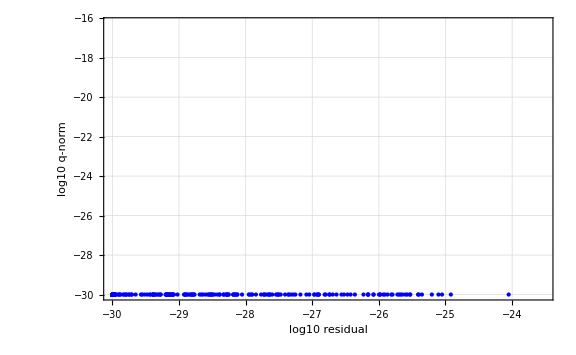

```mathematica
ResidualQNormPlot[search]
```

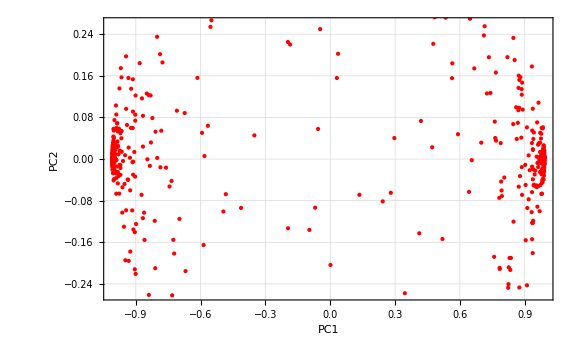

```mathematica
PCASolutionPlot[search]
```

```mathematica
If[Nflavours == 2, TwoFlavorSolutionTable[search]]
```

a=lam1111 | b=lam1112 | c=lam1122 | d=lam1222 | e=lam2222
0.59458918 | -0.1584587 | 0.49265516 | 0.1584587 | 0.59458918
0.67947846 | 0.12694807 | -0.21068087 | -0.12694807 | 0.67947846
0.58732629 | 0.12516861 | 0.5279785 | -0.12516861 | 0.58732629
-0.37778909 | 0.53470843 | 0.37778909 | -0.53470843 | -0.37778909
0.6882472 | 3.1837829×10^-17 | 0.22941573 | 0 | 0.6882472
0.36739099 | 0.30375497 | 0.7385889 | -0.30375497 | 0.36739099
0.69899226 | -0.02688549 | 0.14619839 | 0.02688549 | 0.69899226
0.54701803 | 0.22617893 | -0.54701803 | -0.22617893 | 0.54701803
0.5808618 | 0.076681392 | 0.55985628 | -0.076681392 | 0.5808618
0.6322311 | -0.19484366 | 0.35304331 | 0.19484366 | 0.6322311
0.63947521 | 0.17134613 | 0.35131739 | -0.17134613 | 0.63947521
0.63712886 | -0.12430916 | 0.39651998 | 0.12430916 | 0.63712886
0.66691221 | 0.14407254 | 0.26256889 | -0.14407254 | 0.66691221
0.68660956 | 0.11287235 | 0.17791655 | -0.11287235 | 0.68660956
0.70122603 | 0.039213983 | 0.11614055 | -0.039213983 | 0.70122603
0.68982573 | -0.080907634 | 0.18758686 | 0.080907634 | 0.68982573
0.68836189 | -0.070036795 | 0.20616867 | 0.070036795 | 0.68836189
0.69466503 | 0.038146858 | 0.17880331 | -0.038146858 | 0.69466503
0.68298519 | -0.038237945 | 0.25325517 | 0.038237945 | 0.68298519
0.69044037 | -0.022976573 | 0.21337375 | 0.022976573 | 0.69044037
0.68574756 | 0.0028542872 | 0.24389396 | -0.0028542872 | 0.68574756
0.68847498 | 0.0026180064 | 0.2280147 | -0.0026180064 | 0.68847498
0.69122407 | -0.007511564 | 0.21048927 | 0.007511564 | 0.69122407
0.68210502 | 0.017910367 | 0.26234315 | -0.017910367 | 0.68210502
0.67785134 | 0.017124471 | 0.28363468 | -0.017124471 | 0.67785134
0.67552919 | 0.035134763 | 0.2912932 | -0.035134763 | 0.67552919
0.69620052 | 0.042559453 | 0.16427736 | -0.042559453 | 0.69620052
0.69565657 | -0.056533482 | 0.16041132 | 0.056533482 | 0.69565657
0.69285885 | -0.076663822 | 0.16774548 | 0.076663822 | 0.69285885
0.70220625 | -0.027193789 | 0.11105743 | 0.027193789 | 0.70220625
0.66696943 | 0.11541687 | 0.28924287 | -0.11541687 | 0.66696943
0.68285256 | -0.12377832 | 0.19178791 | 0.12377832 | 0.68285256
0.70521709 | -0.0090451843 | 0.071931011 | 0.0090451843 | 0.70521709
0.68573472 | -0.13288615 | 0.15562243 | 0.13288615 | 0.68573472
0.62290377 | 0.039741271 | 0.46991813 | -0.039741271 | 0.62290377
0.63964696 | -0.16291334 | 0.35863914 | 0.16291334 | 0.63964696
0.68357629 | -0.15481069 | 0.13234128 | 0.15481069 | 0.68357629
0.6869715 | -0.14977905 | 0.10617345 | 0.14977905 | 0.6869715
0.61256064 | -0.17413883 | 0.43461507 | 0.17413883 | 0.61256064
0.59932656 | 0.16602161 | 0.4759086 | -0.16602161 | 0.59932656
0.6287414 | 0.23177135 | 0.31926883 | -0.23177135 | 0.6287414
0.62806212 | 0.24340356 | 0.30427844 | -0.24340356 | 0.62806212
0.60728754 | 0.24791309 | 0.37347273 | -0.24791309 | 0.60728754
0.70196378 | -0.084533248 | -0.014210977 | 0.084533248 | 0.70196378
0.67480697 | -0.204293 | 0.076156698 | 0.204293 | 0.67480697
0.57262017 | 0.26690707 | 0.44914753 | -0.26690707 | 0.57262017
0.50542855 | -0.096336375 | 0.68594648 | 0.096336375 | 0.50542855
0.54997645 | -0.28072693 | 0.48727465 | 0.28072693 | 0.54997645
0.69713085 | 0.11427373 | -0.0435911 | -0.11427373 | 0.69713085
0.46299015 | 0.098281594 | 0.74294124 | -0.098281594 | 0.46299015

```mathematica
If[Nflavours == 2, TwoFlavorProjectionPlots[search]]
```

-Graphics-

## 10. Symbolic check of the hypercubic branch

As a sanity check, the hypercubic ansatz lambda_iiii = u, lambda_iijj = w, all other components zero, should satisfy the maximal entropy and Lie-chain equations for every N. This cell substitutes that branch into the constructed equations.

```mathematica
CheckHypercubicBranch[model, maxLieOrder]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## 11. One-command workflow

The whole procedure can be rerun with a single command. Change Nflavours, precision, maxLieOrder, and samples above, then evaluate this cell. By default RunWorkflow now uses the fast known-branch sampler rather than the expensive random Lie-chain optimizer.

```mathematica
workflow = RunWorkflow[
  Nflavours, maxLieOrder,
  "Precision" -> precision,
  "Method" -> "KnownBranches",
  "Branches" -> If[Nflavours == 3, {"Hypercubic"}, {"Hypercubic", "Simplex"}],
  "CountPerBranch" -> 250,
  "RandomRotations" -> True,
  "Samples" -> samples,
  "WorkingPrecision" -> workingPrecision,
  "EpsilonValue" -> 1,
  "KappaValue" -> 1
];
```

N = 3

Number of independent symmetric quartic variables: 15

Number of independent M_{1|3} equations: 5

OptionValue::nodef: Unknown option Method for RunWorkflow.

OptionValue::nodef: Unknown option Branches for RunWorkflow.

OptionValue::nodef: Unknown option CountPerBranch for RunWorkflow.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

$Aborted

## Important caveat

The all-order condition contains infinitely many Lie derivatives. A numerical notebook cannot literally impose infinitely many equations. The intended workflow is to impose a finite maxLieOrder, find candidate points, then increase maxLieOrder and verify that the candidates persist and that their residuals remain below precision. For small N one can replace the numerical search by exact real algebraic methods such as Resolve or Reduce, but those computations become expensive quickly.